```mathematica
Clear[x, y]
f = E^x + E^Sin[x y^3]
%//TeXForm
```

ⅇ^x+ⅇ^Sin[x y^3]

e^{\sin \left(x
   y^3\right)}+e^x

```mathematica
dfdx = D[f,x] 
%//TeXForm
```

ⅇ^x+ⅇ^Sin[x y^3] y^3 Cos[x y^3]

y^3 e^{\sin \left(x
   y^3\right)} \cos \left(x
   y^3\right)+e^x

```mathematica
dfdy = D[f,y]
%//TeXForm
```

3 ⅇ^Sin[x y^3] x y^2 Cos[x y^3]

3 x y^2 e^{\sin \left(x
   y^3\right)} \cos \left(x
   y^3\right)

```mathematica
x = Cos[ξ^2] + Sin[η + 1] + 5ξ
%//TeXForm
```

5 ξ+Cos[ξ^2]+Sin[1+η]

\sin (\eta +1)+\cos \left(\xi
   ^2\right)+5 \xi

```mathematica
y = Sin[ξ^3] - Cos[η^2] + 7η
%//TeXForm
```

7 η-Cos[η^2]+Sin[ξ^3]

-\cos \left(\eta ^2\right)+7
   \eta +\sin \left(\xi
   ^3\right)

```mathematica
dxdξ = D[x, ξ]
%//TeXForm
```

5-2 ξ Sin[ξ^2]

5-2 \xi  \sin \left(\xi
   ^2\right)

```mathematica
dxdη = D[x, η]
%//TeXForm
```

Cos[1+η]

\cos (\eta +1)

```mathematica
dydξ = D[y, ξ]
%//TeXForm
```

3 ξ^2 Cos[ξ^3]

3 \xi ^2 \cos \left(\xi
   ^3\right)

```mathematica
dydη = D[y, η]
%//TeXForm
```

7+2 η Sin[η^2]

2 \eta  \sin \left(\eta
   ^2\right)+7

```mathematica
dfdξ = dfdx dxdξ + dfdy dydξ
```

9 ⅇ^Sin[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] ξ^2 Cos[ξ^3] Cos[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] (5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^2+(5-2 ξ Sin[ξ^2]) (ⅇ^(5 ξ+Cos[ξ^2]+Sin[1+η])+ⅇ^Sin[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] Cos[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] (7 η-Cos[η^2]+Sin[ξ^3])^3)

```mathematica
dfdη = dfdx dxdη + dfdy dydη
```

3 ⅇ^Sin[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] Cos[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] (7+2 η Sin[η^2]) (5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^2+Cos[1+η] (ⅇ^(5 ξ+Cos[ξ^2]+Sin[1+η])+ⅇ^Sin[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] Cos[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] (7 η-Cos[η^2]+Sin[ξ^3])^3)

```mathematica
gradF = Grad[f, {ξ, η}];
%//TeXForm

gradChainF = {dfdξ, dfdη};

gradChainF - gradF//Simplify
```

{0,0}

```mathematica
{0,0}
```

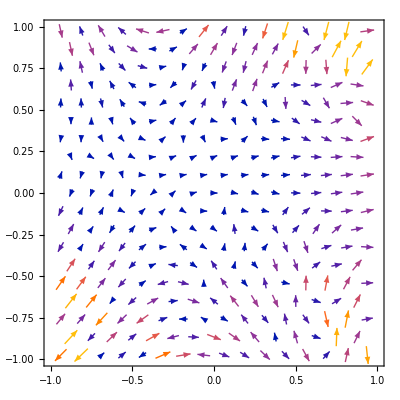

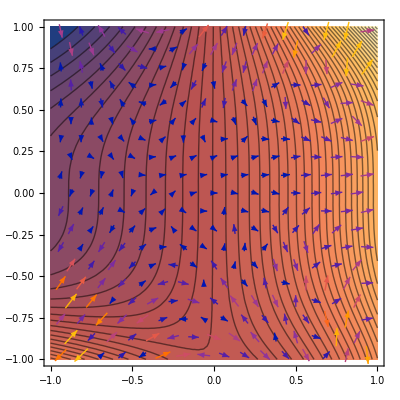

```mathematica
a = VectorPlot[gradF, {ξ, -1, 1}, {η, -1, 1}, VectorScaling->Automatic]
b=ContourPlot[f,{x,-1,1},{y,-1,1},Contours->50];

Show[b, a]
```